```mathematica
PlotCondition[cond_, size_:10] :=RegionPlot[cond, {x, -size, size}, {y, -size, size}]

ClearAll[PlotComplex]
PlotComplex[func_, size_:10,opha_:5,prec_:120,offX_:0,offY_:0] := {n=0; m=0;Monitor[
{RegionPlot[True,{x, -size+offX, size+offX}, {y, -size+offY, size+offY},ColorFunction->Function[{x,y},{funcval=func[x+ⅈ*y];Hue[Arg[funcval]/(2π),1,1,1/(1+Abs[funcval]/opha)],n=y-size+offY}],ColorFunctionScaling->False,ImageSize -> Large, PlotPoints-> prec,PlotLabel->StringForm[ToString[Definition[func],InputForm]]],RegionPlot[True,{x, -size, size}, {y, -size, size},ColorFunction->Function[{x,y},{Hue[Arg[x+ⅈ*y]/(2π),1,1,1/(1+Abs[x+ⅈ*y]/opha)],m=y-size}],ColorFunctionScaling->False,ImageSize -> Large,PlotPoints-> Min[prec,120],PlotLabel->"f[z_] := z"]},
Grid[{Text[Style["Calculating Points :",Darker[Blue,0.66]]],ProgressIndicator[n+m,{-2*size,2*size}]},{n,m}]]}
```

```mathematica
ClearAll[PlotComplex]
PlotComplex[func_,prec_:100,opha_:5,OptionsPattern[{PlotRange->{{0,5},{0,5}},Dump->False}]]:=(Module[{range,colorfunction,graphic},
range=OptionValue[PlotRange];
If[MatchQ[range,{{_,_},{_,_}}],,Throw["PlotRange must be {{a,b},{c,d}}, where a,b,c,d are Real Numbers"]];

colorfunction=Function[{x,y},Module[{funcval=func[x+ⅈ*y]},Hue[Arg[funcval]/(2π),1,1,1/(1+Abs[funcval]/opha)]]];
graphic=RegionPlot[True,{x,range[[1,1]] ,range[[1,2]]}, {y,range[[2,1]],range[[2,2]]},ColorFunction->colorfunction,PlotRange->OptionValue[PlotRange],ColorFunctionScaling->False,ImageSize -> Large,PlotPoints-> prec,PlotLabel->StringForm[ToString[Definition[func],InputForm]]];

If[TrueQ[OptionValue[Dump]],
Module[{path,n,oldpath},
oldpath =Directory[];
path=StringJoin[ToString[ParentDirectory[NotebookDirectory[]]],"\PDFs"];
SetDirectory[path];
n=1;
While[FileExistsQ[StringJoin["new graphic",ToString[n],".pdf"]],
n++;
];
path=StringJoin[path,"\\new graphic",ToString[n],".pdf"];
Export[path,graphic,"AllowRasterization"->True,ImageResolution->(Max[600,prec])];
Print[StringJoin["dumped graphic to '",path,"'"]]
]
,graphic]

])
```

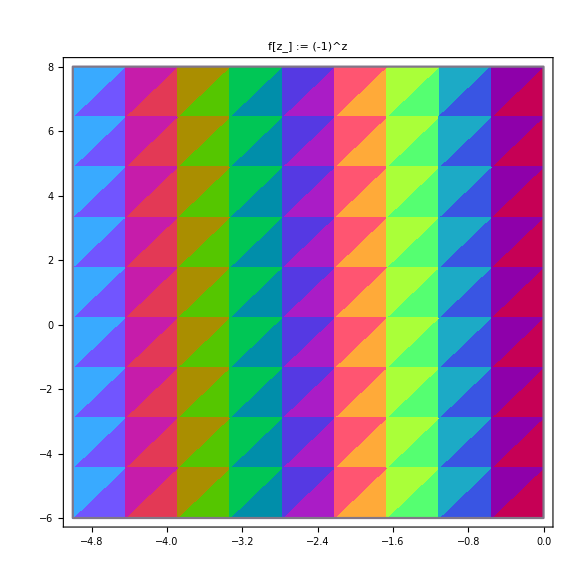

```mathematica
ClearAll[f]
f[z_]:=(-1)^z
PlotComplex[f,10,5,PlotRange->{{-5,0},{-6,8}},Dump->False]
```

```mathematica
ClearAll[f]
f[z_]:=Sin[z]^2
PlotComplex[f,π,1,20]
```

{{-Graphics-,-Graphics-}}